```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/humayrajeba/Documents/Wolfram Mathematica/processed_data_dBm"];
data=Import["updated_vr_2.txt","Table"];
micromobility=data⟦All,2⟧;
SetDirectory["/Users/humayrajeba/Documents/Wolfram Mathematica/THzBlock"];
data=Import["Set3_H=135cm_L13=450cm_L12=300cm/DATA_UNCAL_Meas22","Table"];
avgParam=20;
percentage=5;
blockage=data⟦All,2⟧;
```

```mathematica
micromobility
blockage
```

```mathematica
(*Calculate the weighted signal and its exponential moving average*)
block1=10*Log10[blockage]
```

```mathematica
micro1=Take[micromobility]
```

-Graphics-

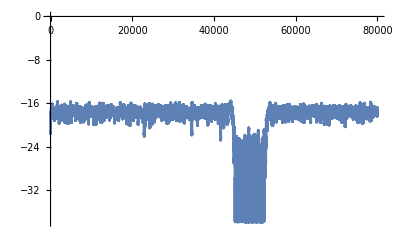

```mathematica
microPeriodogram=PeriodogramArray@micro1
ListLinePlot[micro1,PlotRange->All]

blockPeriodogram=PeriodogramArray@block1
ListLinePlot[block1+35,PlotRange->All]
```

```mathematica
microPeriodogram=PeriodogramArray[micro1];
blockPeriodogram=PeriodogramArray[block1];

ListLinePlot[{micro1,block1+37},PlotRange->All,PlotLegends->{"Micro1","Block1"}]
```

-Graphics-

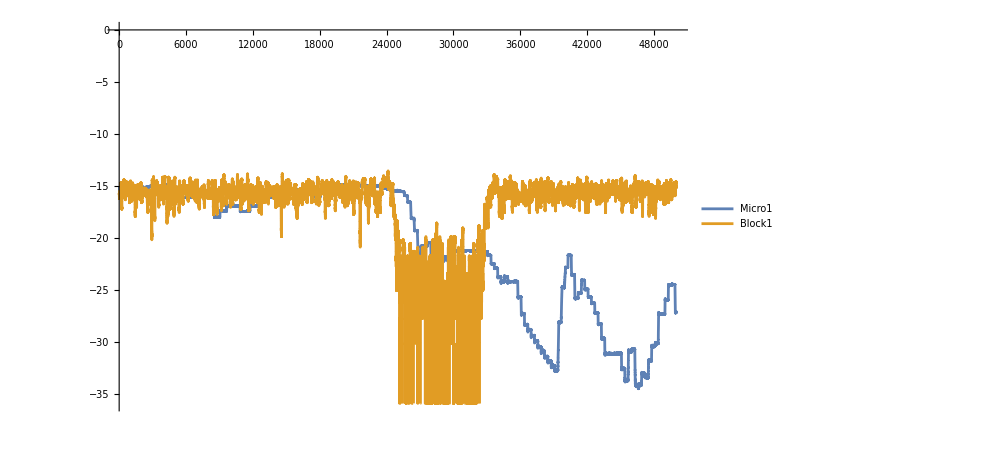

```mathematica
ListLinePlot[{micro1[[30000;;80000]],block1[[20000;;70000]]+37},PlotRange->All,PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro1","Block1"},{0.6,0.8}]]
```

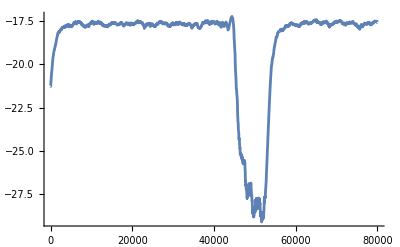

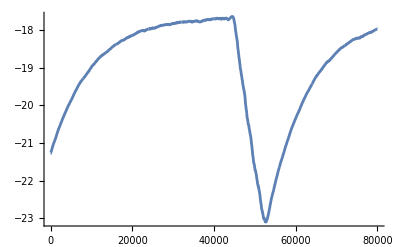

```mathematica
block=block1+35
decayRate1=0.001;
movingAvg1=Re[ExponentialMovingAverage[block,decayRate1]]
ListLinePlot[movingAvg1,PlotRange->All]
decayRate2=0.0001;
movingAvg2=Re[ExponentialMovingAverage[block,decayRate2]]
ListLinePlot[movingAvg2,PlotRange->All]
```

```mathematica
movingAvg3=Re[ExponentialMovingAverage[micromobility,decayRate1]]
ListLinePlot[movingAvg3,PlotRange->All]
movingAvg4=Re[ExponentialMovingAverage[micromobility,decayRate2]]
ListLinePlot[movingAvg4,PlotRange->All]
```

-Graphics-

-Graphics-

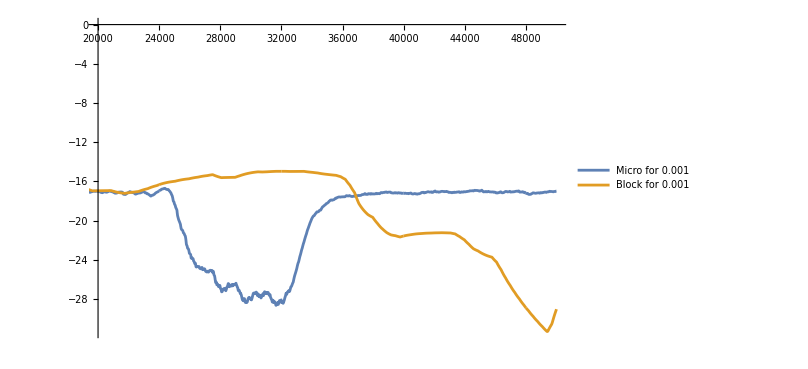

```mathematica
ListLinePlot[{movingAvg1[[20000;;70000]]+0.5,movingAvg3[[20000;;70000]]},PlotRange->{{20000,50000},All},PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro for 0.001","Block for 0.001"},{0.8,0.7}]]
```

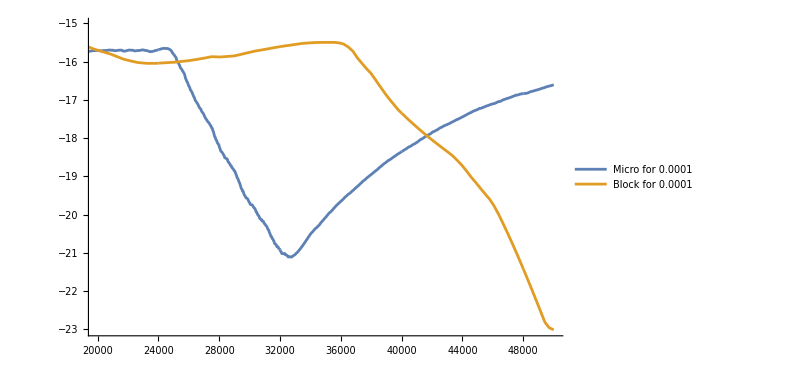

```mathematica
ListLinePlot[{movingAvg2[[20000;;70000]]+1.99,movingAvg4[[20000;;70000]]},PlotRange->{{20000,50000},All},PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro for 0.0001","Block for 0.0001"},{0.4,0.6}]]
```

```mathematica
(*Initialize the list to store the sum of periodograms without decay rate*)
sumPeriodograms={};

(*Calculate the number of segments*)
numSegments=Quotient[Length[block],500];

(*Loop through each segment*)
For[i=1,i<=numSegments,i++,
(*Extract the i^th segment of 500 values*)
blockSegment=Take[block,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram=PeriodogramArray[blockSegment];
(*Sum up the values of the periodogram*)
sumPeriodogram=Total[periodogram];
(*Append the sum to the list*)
AppendTo[sumPeriodograms,sumPeriodogram];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms
```

{156999.,159843.,155849.,153551.,158178.,156125.,156326.,159035.,157153.,157208.,156418.,149249.,155707.,152467.,156637.,161624.,159546.,156356.,155529.,151034.,153419.,156424.,154742.,155509.,155609.,160251.,159306.,159335.,153034.,153201.,153846.,155668.,158504.,155335.,153345.,161077.,152272.,155984.,159612.,153391.,155270.,152797.,152931.,152132.,157041.,167167.,151092.,156117.,157649.,158272.,158941.,153130.,152008.,153188.,157202.,156422.,157334.,159512.,155373.,153678.,156579.,153470.,156628.,153892.,157786.,159170.,155919.,152878.,161399.,157743.,152836.,161951.,162691.,153864.,149983.,153853.,151807.,159749.,153673.,149952.,157470.,154153.,156199.,159331.,161516.,148977.,172525.,139896.,145235.,218742.,338821.,383502.,382763.,349751.,357320.,456513.,371662.,369374.,507946.,421076.,389181.,407920.,462813.,421187.,373314.,247803.,166089.,140815.,165437.,155582.,154501.,157315.,158951.,161149.,153546.,158947.,153414.,153265.,158005.,157873.,157948.,159537.,150529.,151908.,154146.,157435.,154610.,153991.,149352.,152559.,157103.,156552.,157422.,152207.,150130.,163362.,156734.,155817.,151588.,151227.,154670.,151846.,159991.,153676.,156325.,154975.,153288.,152011.,160342.,159806.,161912.,154936.,158756.,153378.,154618.,153180.,159240.,152576.,150147.,154137.}

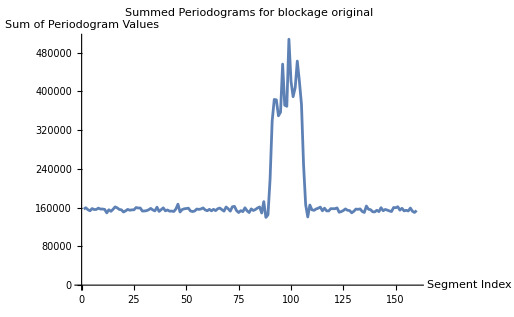

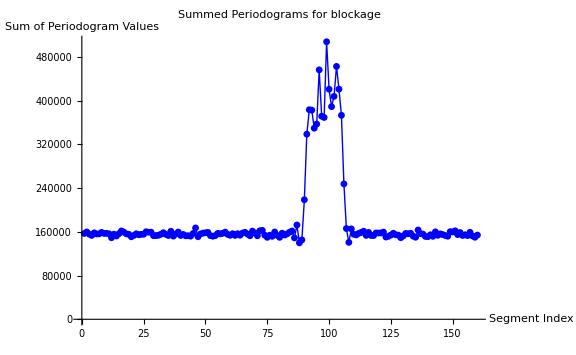

```mathematica
(*Plot the summed periodograms for blockage trace*)
ListLinePlot[sumPeriodograms,PlotRange->All,
PlotLabel->"Summed Periodograms for blockage original",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for blockage",AxesLabel->{"Segment Index","Sum of Periodogram Values"},ImageSize->Large]
```

```mathematica
(*Initialize the list to store the sum of periodograms without decay rate*)
sumPeriodograms1={};

(*Calculate the number of segments*)
numSegments1=Quotient[Length[micromobility],500];

(*Loop through each segment*)
For[i=1,i<=numSegments1,i++,
(*Extract the i^th segment of 500 values*)
microSegment1=Take[micromobility,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram1=PeriodogramArray[microSegment1];
(*Sum up the values of the periodogram*)
sumPeriodogram1=Total[periodogram1];
(*Append the sum to the list*)
AppendTo[sumPeriodograms1,sumPeriodogram1];]

(*Output the list of summed periodograms for micromobility*)
sumPeriodograms1
```

{110764.,113099.,112409.,112518.,112847.,112930.,112930.,113073.,113375.,114266.,115440.,114230.,111619.,110369.,110191.,110253.,110323.,111403.,111457.,112122.,111360.,112838.,115827.,117301.,117310.,120906.,117087.,112930.,112914.,113065.,112845.,113661.,113376.,113396.,113276.,114205.,113995.,114164.,113676.,112225.,112249.,112544.,112460.,112748.,112757.,113757.,115876.,114848.,114528.,113854.,117668.,127287.,127735.,126320.,123353.,125622.,125661.,122942.,120225.,117935.,115107.,113582.,113050.,114521.,114493.,113237.,113028.,113584.,113270.,123476.,129750.,128693.,129337.,125412.,121774.,120821.,121819.,160528.,151978.,145760.,143240.,145792.,151967.,147318.,142893.,136687.,131499.,127308.,124548.,124776.,121401.,120865.,117848.,115921.,114680.,127985.,122033.,120640.,111287.,110128.,110537.,112898.,111275.,111791.,112473.,112205.,112178.,115775.,117431.,119389.,120101.,127979.,154592.,206539.,218705.,212360.,245363.,248779.,240745.,234370.,224851.,224471.,224764.,224993.,224981.,226645.,237509.,259274.,286596.,285838.,292110.,308287.,371855.,410361.,438263.,464276.,487343.,512787.,508227.,341484.,250392.,281309.,323973.,298384.,329138.,360931.,416048.,476202.,483561.,482907.,530136.,511733.,514693.,573362.,551124.,486434.,438098.,371564.,321117.,312718.,393334.,448816.,446130.,410834.,265968.,241591.,209184.,189641.,183126.,171188.,156394.,156577.,172259.,210992.,251855.,292820.,265698.,250168.,237192.,281891.,359361.,391036.,448262.,447457.,441284.,413631.,326120.,256982.,237157.,258532.,285771.,307680.,296892.,275844.,328871.,320688.,268824.,281199.,269343.,368488.,378475.,337430.,337512.,297020.,237550.,178810.,165463.,163649.,155473.,152302.,158681.,136468.,123081.,119698.,122392.,124074.,126612.,124231.,123124.,135473.,171739.,202541.,232026.,243552.,267185.,270423.,269153.,272510.,249904.,220735.,196090.,193676.,197034.,184562.,163574.,148738.,165941.,157755.,144749.,138858.,136693.,140112.,136631.,137526.,141902.,141887.,141873.,141534.,145946.,173520.,255075.,343622.,350683.,347893.,363093.,382578.,407858.,375028.,243260.,258626.,291808.,346638.,349468.,332059.,358915.,401529.,421646.,353750.,319358.,345176.,367043.,353076.,377634.,384018.,383565.,383811.,384001.,383969.,383605.,412312.,424773.,387859.,384457.,407480.,380165.,203102.,193285.,176043.,176613.,176614.,176638.,176618.,176687.,176749.,170387.,175910.,183699.,184024.,190016.,202150.,223136.,224651.,215644.,215752.,206700.,205548.,235856.,249263.,240562.,251847.,240665.,227548.,227272.,225650.,430923.,473724.,474531.,470093.,476100.,481126.,473045.,482320.,506236.,524062.,525187.,532982.,506109.,463044.,469141.,504213.,495920.,489460.,460006.,458415.,458429.,447475.,436046.,422896.,407570.,395201.,385780.,384664.,381111.,385416.,437400.,452406.,452874.,453228.,446008.,443673.,442696.,442710.,443122.,442951.,461078.,465095.,444992.,432315.,411487.,442957.,466087.,255508.,173145.,173236.,189748.,178755.,168457.,183755.,208055.,208059.,215490.,215537.,215784.,255447.,262995.,220582.,233316.,219467.,208538.,198935.,183921.,198597.,229444.,258806.,288339.,357834.,470014.,482659.,525795.,538093.,427049.,443217.,443075.,443062.,427078.,503690.,457805.,330413.,292450.,289644.,258902.,239992.,236902.,239965.,288695.,386047.,482249.,501329.,547924.,564641.,587376.,501582.,395831.,321034.,270714.,235667.,261467.,255515.,238722.,225713.,210007.,207907.,209168.,237840.,337962.,333263.,470082.,654520.,648956.,571950.,449981.,363881.,305823.,251423.,216421.,190634.,181874.,170687.,216466.,224432.,223364.,223938.,216127.,204881.,204386.,212775.,202852.,209615.,223390.,222332.,223560.,223703.,222177.,256419.,241729.,252612.,256539.,256125.,250833.,243389.,234153.,227220.,218171.,210029.,219564.,207990.,174799.,157314.,155129.,144334.,147740.,144579.,142915.,142195.,140678.,142013.,131096.,113157.,113873.,116455.,119476.,120133.,123969.,122058.,122415.,122823.,118623.,125871.,126440.,123392.,118781.,118448.,118413.,115322.,115161.,118432.,116249.,114138.,112885.,112426.,112564.,117508.,118084.,116134.,116722.,119345.,120806.,117948.,119401.,117618.,114738.,115274.,112925.,112831.,112129.,111163.,111976.,112085.,114814.,117936.,123140.,122075.,121044.,122833.,136851.,166036.,163039.,179669.,214940.,230917.,238576.,259610.,259745.,259776.,259724.,268536.,244180.,236510.,227497.,215267.,228496.,207555.,216587.,209775.,199584.,137965.,126406.,120953.,116902.,114010.,112963.,115079.,111335.,111045.,114965.,121700.,121398.,121394.,121384.,121223.,121341.,122309.,122238.,121747.,122060.,125066.,128884.,140621.,145160.,149038.,155360.,167047.,174713.,176313.,176329.,179490.,181603.,181511.,185277.,240172.,237096.,205331.,189827.,192008.,200603.,210468.,242908.,269051.,282250.,290024.,353609.,435185.,376244.,366809.,316093.,336636.,313291.,240027.,254888.,292597.}

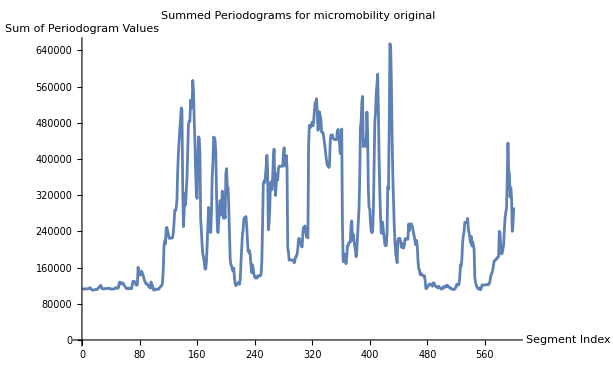

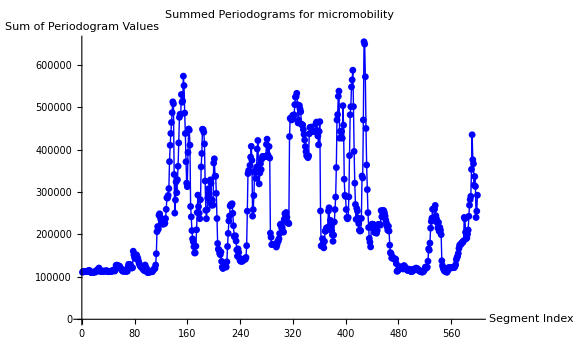

```mathematica
(*Plot the summed periodograms*)
ListLinePlot[sumPeriodograms1,PlotRange->All,
PlotLabel->"Summed Periodograms for micromobility original",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms1,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for micromobility",AxesLabel->{"Segment Index","Sum of Periodogram Values"},ImageSize->Large]
```

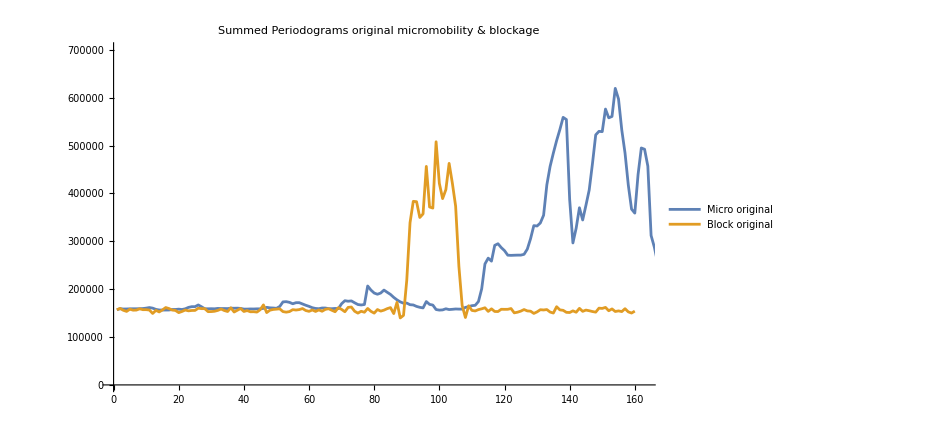

```mathematica
ListLinePlot[{sumPeriodograms1+46150,sumPeriodograms},PlotRange->{{0,163},All},PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms original micromobility & blockage",PlotLegends->Placed[{"Micro original","Block original"},{0.2,0.8}]]
```

{211545.,188097.,177028.,166887.,163123.,160396.,158995.,158134.,157115.,157829.,157540.,154939.,154395.,153467.,154138.,156403.,158057.,157778.,157350.,155078.,153549.,155176.,154684.,154122.,154827.,156413.,157523.,157972.,156831.,155834.,154735.,154643.,155983.,156001.,154740.,156609.,156031.,155343.,155719.,155671.,156020.,154754.,153155.,153714.,154276.,157113.,157423.,156042.,156178.,156287.,157392.,156923.,155327.,153772.,154483.,155178.,155049.,157141.,157238.,155249.,155761.,155001.,155348.,154839.,155955.,156027.,156913.,155423.,156733.,158259.,156127.,155680.,159391.,158880.,155068.,153817.,153450.,154751.,154503.,153508.,154550.,153953.,155476.,157063.,155718.,155836.,158189.,157008.,149628.,158454.,203362.,255011.,302677.,321472.,329173.,356038.,377692.,366629.,384980.,408684.,393803.,394350.,399039.,416630.,400388.,357087.,286973.,227564.,196057.,181796.,170401.,164381.,162165.,162037.,159703.,158142.,157530.,155280.,155724.,156423.,156984.,157846.,155972.,154550.,154018.,153983.,155241.,154590.,153196.,152137.,153375.,154408.,155547.,154277.,153844.,154651.,157715.,156345.,155033.,153664.,153298.,152931.,153858.,155198.,155762.,155011.,154455.,153867.,155059.,156405.,158784.,159289.,157373.,155831.,155496.,154552.,155409.,155037.,153526.,153331.}

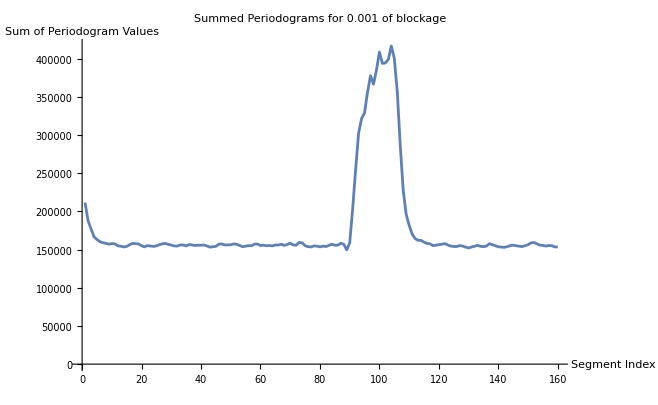

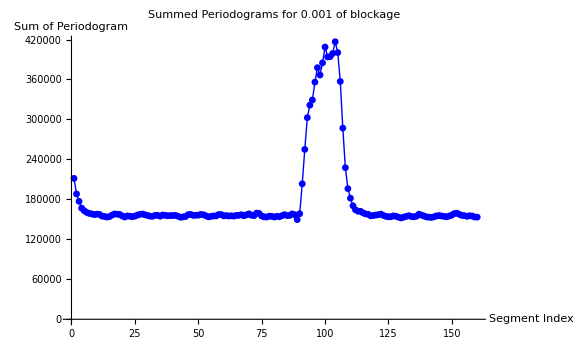

```mathematica
(*Initialize the list to store the sum of periodograms with 0.001 decay rate for blockage*)
sumPeriodograms2={};

(*Calculate the number of segments*)
numSegments2=Quotient[Length[movingAvg1],500];

(*Loop through each segment*)
For[i=1,i<=numSegments2,i++,
(*Extract the i^th segment of 500 values*)
blockSegment2=Take[movingAvg1,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram2=PeriodogramArray[blockSegment2];
(*Sum up the values of the periodogram*)
sumPeriodogram2=Total[periodogram2];
(*Append the sum to the list*)
AppendTo[sumPeriodograms2,sumPeriodogram2];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms2
(*Plot the summed periodograms for 0.001*)
ListLinePlot[sumPeriodograms2,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.001 of blockage",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms2,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.001 of blockage",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

{109581.,110744.,111453.,111895.,112189.,112478.,112636.,112812.,112925.,113265.,113964.,114389.,113725.,112605.,111655.,111077.,110790.,110714.,111115.,111380.,111509.,111578.,112853.,114372.,115508.,116856.,118143.,116442.,115047.,114223.,113783.,113483.,113551.,113481.,113401.,113595.,113768.,113883.,113947.,113493.,112974.,112763.,112635.,112651.,112708.,112942.,113616.,114359.,114526.,114283.,114983.,117827.,121852.,123926.,124091.,124209.,125045.,124615.,123411.,121533.,119570.,117441.,115789.,114937.,114867.,114453.,113843.,113735.,113315.,115238.,120219.,123602.,125798.,126599.,125036.,123684.,122440.,130105.,140277.,143687.,143637.,143655.,146169.,147821.,146329.,143900.,139869.,135522.,131459.,128773.,126538.,124368.,122276.,120130.,118217.,119519.,121769.,121509.,119137.,115674.,113504.,112986.,112527.,112097.,112113.,112254.,112181.,112974.,114308.,116061.,117491.,119654.,127567.,146924.,174005.,189252.,204486.,221177.,230439.,233719.,230989.,228451.,227008.,226187.,225678.,225724.,227569.,236202.,250867.,264794.,274457.,282887.,305296.,339649.,372359.,402666.,431091.,458241.,482604.,455665.,383489.,329641.,323253.,316215.,315676.,327319.,350920.,388618.,424559.,447204.,468247.,494606.,492355.,519542.,533944.,529248.,502248.,458176.,412991.,369142.}

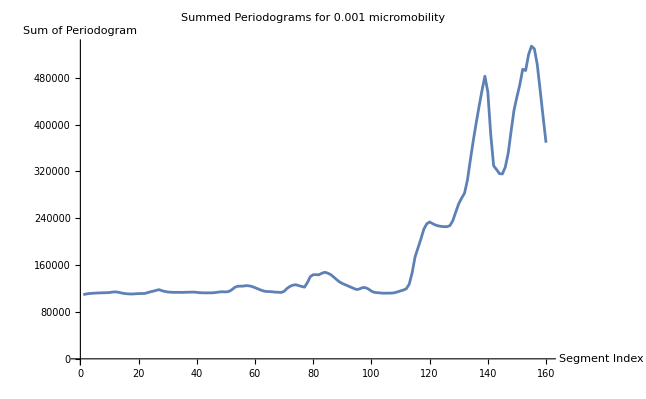

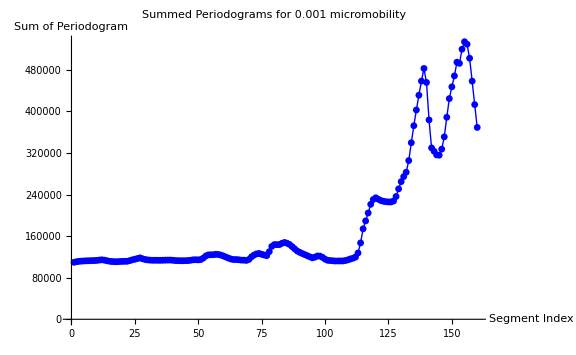

```mathematica
(*Initialize the list to store the sum of periodograms with 0.001 decay rate for micromobility*)
sumPeriodograms3={};

(*Calculate the number of segments*)
numSegments3=Quotient[Length[movingAvg3],500];

(*Loop through each segment*)
For[i=1,i<=numSegments2,i++,
(*Extract the i^th segment of 500 values*)
blockSegment3=Take[movingAvg3,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram3=PeriodogramArray[blockSegment3];
(*Sum up the values of the periodogram*)
sumPeriodogram3=Total[periodogram3];
(*Append the sum to the list*)
AppendTo[sumPeriodograms3,sumPeriodogram3];]

(*Output the list of summed periodograms for micromobility trace*)
sumPeriodograms3
(*Plot the summed periodograms for 0.001*)
ListLinePlot[sumPeriodograms3,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.001 micromobility",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms3,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.001 micromobility",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

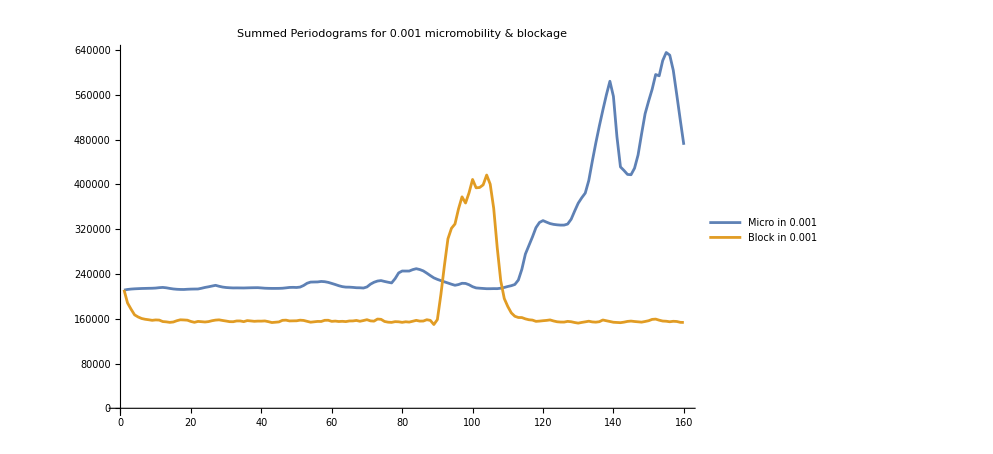

```mathematica
ListLinePlot[{sumPeriodograms3+101495,sumPeriodograms2},PlotRange->All,PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms for 0.001 micromobility & blockage",PlotLegends->Placed[{"Micro in 0.001","Block in 0.001"},{0.2,0.8}]]
```

{224595.,220873.,217723.,214243.,211257.,208389.,205702.,203166.,200697.,198544.,196413.,194067.,191968.,189922.,188138.,186701.,185382.,183975.,182586.,181021.,179499.,178407.,177166.,175956.,174949.,174140.,173402.,172669.,171802.,170928.,170027.,169252.,168691.,168070.,167310.,166910.,166345.,165737.,165268.,164797.,164387.,163819.,163166.,162743.,162361.,162301.,162110.,161703.,161429.,161191.,161084.,160859.,160464.,160015.,159785.,159615.,159384.,159425.,159333.,158989.,158867.,158623.,158479.,158263.,158232.,158126.,158142.,157901.,157926.,158070.,157819.,157669.,158026.,158046.,157616.,157335.,157122.,157085.,156953.,156710.,156674.,156501.,156566.,156697.,156539.,156544.,156752.,156740.,155821.,156480.,161610.,168925.,177424.,184603.,191149.,199380.,208111.,214173.,222238.,231512.,237604.,244363.,251169.,259417.,264720.,266293.,262631.,256436.,250670.,245861.,240849.,236242.,232111.,228385.,224560.,220903.,217513.,214041.,211008.,208220.,205604.,203199.,200606.,198093.,195769.,193607.,191750.,189791.,187810.,185886.,184319.,182886.,181600.,180118.,178756.,177586.,176841.,175706.,174570.,173407.,172368.,171366.,170546.,169897.,169241.,168470.,167731.,167002.,166485.,166098.,165908.,165640.,165071.,164511.,164031.,163494.,163155.,162735.,162168.,161706.}

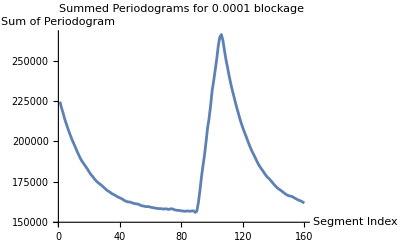

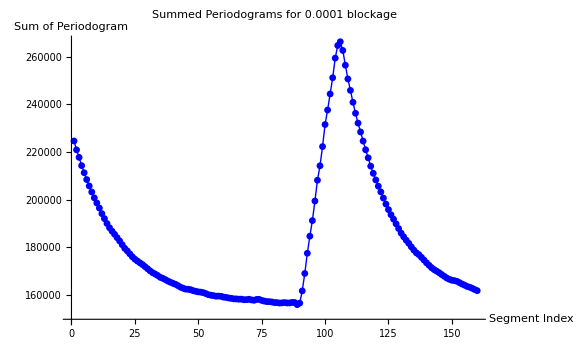

```mathematica
(*Initialize the list to store the sum of periodograms with 0.0001 decay rate for blockage*)
sumPeriodograms4={};

(*Calculate the number of segments*)
numSegments4=Quotient[Length[movingAvg2],500];

(*Loop through each segment*)
For[i=1,i<=numSegments4,i++,
(*Extract the i^th segment of 500 values*)
blockSegment4=Take[movingAvg2,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram4=PeriodogramArray[blockSegment4];
(*Sum up the values of the periodogram*)
sumPeriodogram4=Total[periodogram4];
(*Append the sum to the list*)
AppendTo[sumPeriodograms4,sumPeriodogram4];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms4
(*Plot the summed periodograms for 0.0001*)
ListLinePlot[sumPeriodograms4,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.0001 blockage",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms4,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.0001 blockage",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

{109489.,109632.,109775.,109911.,110042.,110182.,110313.,110447.,110575.,110729.,110936.,111137.,111218.,111204.,111155.,111108.,111070.,111045.,111079.,111112.,111143.,111167.,111339.,111596.,111869.,112202.,112591.,112659.,112672.,112685.,112706.,112720.,112766.,112796.,112820.,112870.,112927.,112982.,113035.,113026.,112984.,112957.,112932.,112919.,112913.,112929.,113009.,113133.,113214.,113250.,113379.,113786.,114469.,115075.,115524.,115945.,116442.,116807.,117042.,117125.,117104.,116964.,116783.,116625.,116534.,116403.,116232.,116100.,115932.,116025.,116589.,117177.,117750.,118240.,118459.,118613.,118706.,119739.,121445.,122735.,123716.,124652.,125826.,126981.,127795.,128399.,128666.,128687.,128528.,128339.,128089.,127742.,127319.,126802.,126231.,125974.,125953.,125715.,125226.,124486.,123769.,123186.,122622.,122063.,121568.,121117.,120667.,120341.,120143.,120073.,120054.,120184.,121076.,123576.,127630.,131338.,135429.,140137.,144593.,148651.,152095.,155304.,158395.,161370.,164224.,166997.,169839.,173348.,177697.,182427.,187073.,191791.,198002.,206039.,214888.,224385.,234484.,245156.,256229.,263356.,264496.,263969.,266217.,268114.,270253.,273663.,278729.,286053.,294468.,302598.,311073.,320695.,328071.,337966.,347402.,355192.,360143.,361884.,361286.,358536.,358244.,361441.,365345.,368795.,366757.,360638.,353431.,344634.,335851.,326876.,317657.,308348.,300265.,294237.,291011.,290084.,289859.,288085.,285960.,284017.,286013.,289986.,295946.,302656.,308929.,314788.,316877.,315495.,311893.,308241.,306435.,305957.,306223.,304631.,304729.,305959.,305124.,303457.,302180.,302473.,306471.,308524.,309904.,310417.,308340.,302765.,295294.,288085.,280879.,273790.,267309.,260632.,253162.,245624.,238515.,232028.,226048.,220479.,215118.,210243.,207236.,206188.,206868.,208287.,210479.,213244.,215829.,218387.,220508.,221078.,220486.,219067.,217885.,216647.,214454.,211248.,208345.,206191.,203210.,199928.,196572.,193588.,190612.,187781.,185291.,183038.,180913.,178884.,177008.,175994.,177631.,182885.,189877.,196489.,203069.,210223.,217779.,225873.,228538.,229526.,231473.,235674.,240683.,245074.,249558.,255244.,262361.,267807.,270769.,273570.,277315.,281120.,284953.,289377.,293677.,297788.,301733.,305514.,309123.,313013.,317987.,322105.,324991.,328115.,332094.,328978.,321675.,313995.,306350.,299199.,292474.,286151.,280201.,274602.,269192.,263884.,259480.,255497.,251821.,248969.,247061.,246132.,244715.,243257.,241763.,239655.,238819.,239021.,239315.,239667.,240114.,239684.,239052.,238442.,241072.,250698.,259958.,268783.,277472.,286027.,294204.,302028.,310415.,319146.,328016.,336831.,344835.,351130.,355975.,362060.,368298.,374045.,378601.,382301.,385855.,389046.,391548.,393375.,394390.,394727.,394469.,393994.,393509.,392933.,393567.,396254.,398918.,401484.,403817.,405699.,407522.,409185.,410800.,412334.,414098.,416650.,418411.,419511.,419537.,419633.,421398.,418920.,406011.,392378.,380217.,369161.,357803.,347133.,338985.,332051.,325425.,319541.,313997.,309739.,307484.,304016.,299890.,296110.,291811.,287131.,281941.,276979.,273683.,272263.,272091.,274090.,280604.,289094.,298169.,308225.,315826.,320894.,326404.,331684.,336597.,341676.,348722.,350635.,348264.,345339.,341861.,336817.,331606.,326584.,323147.,323522.,328993.,336017.,344431.,353383.,363295.,371603.,374970.,373875.,369865.,363379.,357052.,352108.,346535.,340439.,333745.,326992.,320564.,315099.,313814.,314665.,317584.,328754.,342187.,353460.,360471.,362681.,360964.,356659.,350069.,341931.,333158.,324261.,316670.,311989.,307302.,302934.,298583.,294010.,289071.,284953.,280932.,276963.,273902.,271211.,268785.,266485.,264216.,262968.,262335.,261503.,261229.,260990.,260647.,260065.,258881.,257512.,255785.,253551.,251558.,249958.,246701.,242349.,237672.,232892.,228164.,223762.,219446.,215312.,211379.,207600.,203904.,199300.,194538.,190195.,186281.,182658.,179480.,176493.,173562.,170925.,168241.,165786.,163796.,161775.,159637.,157486.,155453.,153452.,151445.,149657.,147995.,146318.,144604.,142946.,141372.,139999.,138914.,137799.,136719.,135742.,134996.,134196.,133401.,132705.,131837.,130996.,130144.,129269.,128431.,127569.,126769.,126025.,125379.,124929.,124732.,124639.,124482.,124334.,124522.,125899.,127598.,129526.,132447.,136426.,140582.,145198.,150014.,154673.,159170.,163711.,167773.,170921.,173776.,175846.,177972.,179994.,181049.,182923.,183965.,183171.,180277.,177279.,174163.,171007.,167915.,165022.,162281.,159575.,157079.,155104.,153369.,151723.,150166.,148687.,147283.,145988.,144781.,143631.,142514.,141551.,140821.,140456.,140662.,140944.,141486.,142383.,143746.,145243.,146689.,148115.,149650.,151135.,152601.,155346.,158997.,161832.,163404.,164626.,166128.,167863.,170498.,174331.,178786.,183351.,189081.,197676.,206056.,212867.,218580.,222931.,228002.,229737.,230567.,232507.}

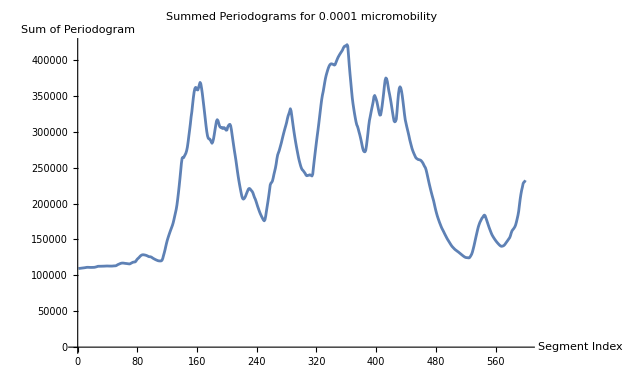

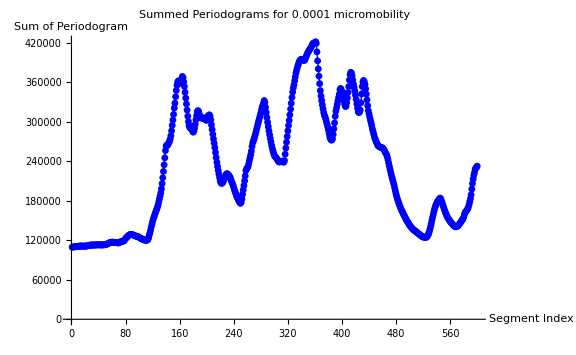

```mathematica
(*Initialize the list to store the sum of periodograms with 0.0001 decay rate for micromobility*)
sumPeriodograms5={};

(*Calculate the number of segments*)
numSegments5=Quotient[Length[movingAvg4],500];

(*Loop through each segment*)
For[i=1,i<=numSegments5,i++,
(*Extract the i^th segment of 500 values*)
blockSegment5=Take[movingAvg4,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram5=PeriodogramArray[blockSegment5];
(*Sum up the values of the periodogram*)
sumPeriodogram5=Total[periodogram5];
(*Append the sum to the list*)
AppendTo[sumPeriodograms5,sumPeriodogram5];]

(*Output the list of summed periodograms for micromobility trace*)
sumPeriodograms5
(*Plot the summed periodograms for 0.0001*)
ListLinePlot[sumPeriodograms5,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.0001 micromobility",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms5,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.0001 micromobility",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

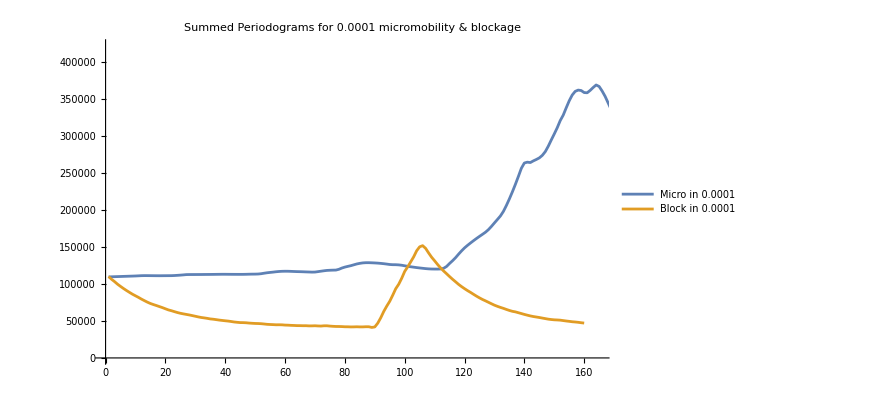

```mathematica
ListLinePlot[{sumPeriodograms5,sumPeriodograms4-114607},PlotRange->{{0,165},All},PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms for 0.0001 micromobility & blockage",PlotLegends->Placed[{"Micro in 0.0001","Block in 0.0001"},{0.3,0.6}]]
```